## Period of trajectories

### Rescaled Hamiltonian

```mathematica
h[p_,q_,mu_,l_,d_]:=1/2(p^2+q^2)+mu/2 √(2 l^2(q^2+d^2 p^2)+1)+1/2
```

### Export contours

```mathematica
ContourPlot[h[p,q,-1,1.5,0.5],{q,-1.5,1.5},{p,-1.5,1.5},Contours->Table[j,{j,-0.2,0.5,0.05}],PlotPoints->100]
```

-Graphics-

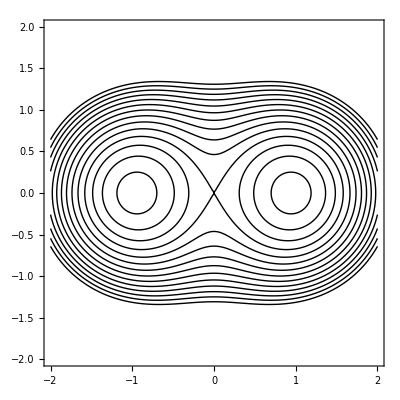

```mathematica
contourLevels=Table[j,{j,-0.2,0.5,0.05}];
plot=ContourPlot[h[p,q,-1,1.5,0.5],{q,-2,2},{p,-2,2},Contours->contourLevels,PlotPoints->100,ContourShading->None]
contours=Cases[plot,GraphicsComplex[coords_,lines__]:>(coords[[#]]&/@Cases[{lines},Line[idx_]:>idx,Infinity]),Infinity][[1]];
```

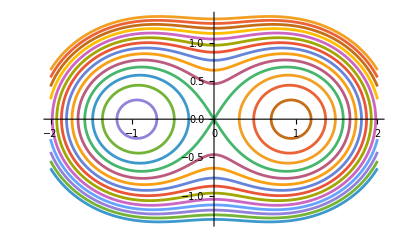

```mathematica
ListLinePlot[contours]
```

```mathematica
Do[Export["d:/contour_"<>ToString[i]<>".csv",contours[[i]]],{i,Length[contours]}]
```

### Initial position

```mathematica
q0[l_]:=√(1/2(l^2-1/l^2))
ef[li_,lf_]:=1/4(li^2-3/li^2)-1/2 lf(li-1/li^3)
```

```mathematica
D[h[p,q,mu,l,d],p]
```

p+(d^2 l^2 mu p)/(√(1+2 l^2 (d^2 p^2+q^2)))

```mathematica
v[p_,q_,mu_,l_,d_]:=p(1+l^2 d^2 mu 1/(√(2 l^2(q^2+d^2 p^2)+1)))
```

### Momentum and velocity

```mathematica
pp[e_,q_,mu_,l_,d_]:=√(-1+2 e+d^2 l^2 mu^2-q^2-mu √(1+l^2 (2 q^2+d^2 (-2+4 e+d^2 l^2 mu^2-2 q^2))))
```

```mathematica
vp[q_,mu_,li_,lf_,d_]:=v[pp[h[0,q0[li],mu,lf,d],q,mu,lf,d],q,mu,lf,d]
```

### Period

```mathematica
T[mu_,li_,lf_,d_]:=NIntegrate[2/vp[q,mu,li,lf,d],{q,-q0[li],q0[li]}]
```

#### Approximate period

```mathematica
Ta[mu_,li_,lf_,d_]:=2π(1-(mu lf^2)/2(1+d^2))
```

#### Numerical

```mathematica
{T[-1,1.5,(√2)/5,0.5],T[1,1.5,(√2)/5,0.5]}
{Ta[-1,1.5,(√2)/5,0.5],Ta[1,1.5,(√2)/5,0.5]}
```

{6.59987,6.00024}

{6.59734,5.96903}

```mathematica
T[1,1.5,-1.5,0.5]
Ta[1,1.5,-1.5,0.5]
```

3.81014

-2.55254

#### Graph - compare delta with delta = 0

```mathematica
pl[li_,d_]:=Plot[{T[-1,li,lf,0],T[1,li,lf,0],T[-1,li,lf,d],T[1,li,lf,d]},{lf,-1.0,1.0},AxesLabel->{"Λ_f","T"},PlotStyle->{{ColorData[116,"ColorList"][[1]],Thick},{ColorData[116,"ColorList"][[1]],Dashed},{ColorData[116,"ColorList"][[2]],Thick},{ColorData[116,"ColorList"][[2]],Dashed}}]
```

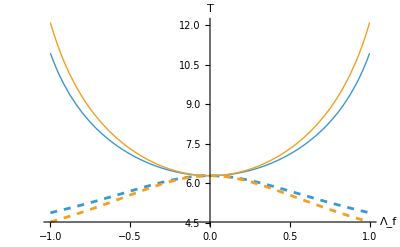

```mathematica
pl[1.5,0.5]
```

```mathematica
pla[li_,d_]:=Plot[{T[-1,li,lf,d],T[1,li,lf,d],Ta[-1,li,lf,d],Ta[1,li,lf,d]},{lf,-1.0,1.0},AxesLabel->{"Λ_f","T"},PlotStyle->{{ColorData[116,"ColorList"][[1]],Thick},{ColorData[116,"ColorList"][[1]],Dashed},{ColorData[116,"ColorList"][[2]],Thick},{ColorData[116,"ColorList"][[2]],Dashed}}]
```

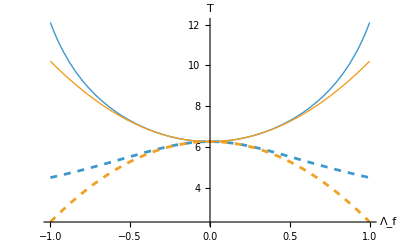

```mathematica
pla[1.5,0.5]
```

#### Ratio between both frequencies for j = 1/2

```mathematica
r[li_,lf_,mu_,d_]:=NIntegrate[2/vp[q,-1,li,lf,d],{q,-q0[li],q0[li]}]/NIntegrate[2/vp[q,mu,li,lf,d],{q,-q0[li],q0[li]}]
```

```mathematica
ra[lf_,mu_,d_]:=Ta[-1,0,lf,d]/Ta[mu,0,lf,d]
```

```mathematica
Table[j*r[1.5,-Sqrt[2]/5,1, 0.5],{j,1,60}]
Table[j*ra[-Sqrt[2]/5,1, 0.5],{j,1,60}]
```

{1.09993,2.19987,3.2998,4.39974,5.49967,6.5996,7.69954,8.79947,9.89941,10.9993,12.0993,13.1992,14.2991,15.3991,16.499,17.5989,18.6989,19.7988,20.8987,21.9987,23.0986,24.1985,25.2985,26.3984,27.4984,28.5983,29.6982,30.7982,31.8981,32.998,34.098,35.1979,36.2978,37.3978,38.4977,39.5976,40.6976,41.7975,42.8974,43.9974,45.0973,46.1972,47.2972,48.3971,49.497,50.597,51.6969,52.7968,53.8968,54.9967,56.0966,57.1966,58.2965,59.3964,60.4964,61.5963,62.6962,63.7962,64.8961,65.996}

{1.10526,2.21053,3.31579,4.42105,5.52632,6.63158,7.73684,8.84211,9.94737,11.0526,12.1579,13.2632,14.3684,15.4737,16.5789,17.6842,18.7895,19.8947,21.,22.1053,23.2105,24.3158,25.4211,26.5263,27.6316,28.7368,29.8421,30.9474,32.0526,33.1579,34.2632,35.3684,36.4737,37.5789,38.6842,39.7895,40.8947,42.,43.1053,44.2105,45.3158,46.4211,47.5263,48.6316,49.7368,50.8421,51.9474,53.0526,54.1579,55.2632,56.3684,57.4737,58.5789,59.6842,60.7895,61.8947,63.,64.1053,65.2105,66.3158}

```mathematica
plr[li_,d_,j_]:=Show[Table[Plot[3NIntegrate[2/vp[q,-1,li,lf,d],{q,-q0[li],q0[li]}]/NIntegrate[2/vp[q,m/j,li,lf,d],{q,-q0[li],q0[li]}],{lf,-1.0,1.0},AxesLabel->{"Λ_f","T"},PlotStyle->{ColorData[116,"ColorList"][[m+j+1]],Thick},PlotStyle->{ColorData[116,"ColorList"][[m+j+1]]}],{m,-j,j}],PlotRange->All]
```

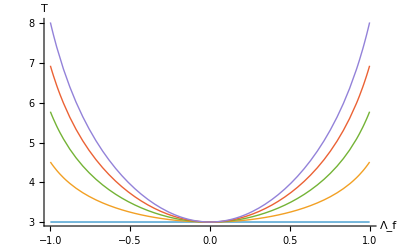

```mathematica
plr[1.5,0.5,2]
```

```mathematica
plt[li_,d_,j_]:=Show[Table[Plot[{NIntegrate[2/vp[q,m/j,li,lf,d],{q,-q0[li],q0[li]}],NIntegrate[2/vp[q,m/j,li,lf,0.0],{q,-q0[li],q0[li]}]},{lf,-1.0,1.0},AxesLabel->{"Λ_f","T"},PlotStyle->{{ColorData[116,"ColorList"][[m+j+1]],Thick},{ColorData[116,"ColorList"][[m+j+1]],Dashed}}],{m,-j,j}],PlotRange->All]
```

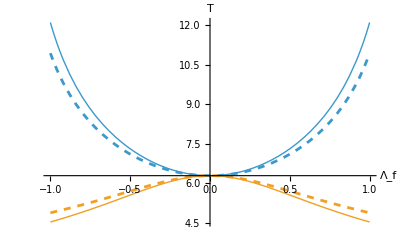

```mathematica
plt[1.5,0.5,1/2]
```

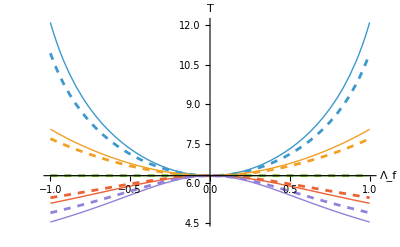

```mathematica
plt[1.5,0.5,2]
```

### Export numbers

```mathematica
exp[li_,d_,j_]:=Partition[Flatten[Table[{lf,Table[Ta[m/j,li,lf,d],{m,-j,j}]},{lf,-1.2,1.2,0.01}]],2j+2]
```

```mathematica
exp[li_,d_,j_]:=Partition[Flatten[Table[{lf,Table[T[m/j,li,lf,d],{m,0,j}]},{lf,-1.6,1.6,0.01}]],j+2]
```

```mathematica
Export["data.txt",exp[1.5,0,1/2],"CSV"]
```

### Critical quench

```mathematica
lfc[li_]:=√(1/4(li^2-1/li^2)+1)
```

```mathematica
lfc[3/2]//N
```

1.20474

```mathematica
eq[j_,th_]:=WignerD[{j,j,-j},th]^2==WignerD[{j,-j,-j},th]^2
```

```mathematica
eq[1/2,th]
```

Sin[th/2]^2==Cos[th/2]^2

```mathematica
FullSimplify[Solve[eq[10,th],th,Reals]]
```

{{th→ConditionalExpression[1/2 π (1+8 C[1]), C[1]∈ℤ]},{th→ConditionalExpression[4 π (-1/8+C[1]), C[1]∈ℤ]},{th→ConditionalExpression[1/2 π (-3+8 C[1]), C[1]∈ℤ]},{th→ConditionalExpression[4 π (3/8+C[1]), C[1]∈ℤ]}}

```mathematica
ct[li_,lf_]:=(2li lf q0[li]^2+1)/(√((2 li^2 q0[li]^2+1)(2 lf^2 q0[li]^2+1)))
```

### Crossing j=1/2

```mathematica
Solve[ct[li,lf]==0,lf]
```

{{lf→-li/(-1+li^4)}}

```mathematica
%/.li->3/2
```

{{lf→-24/65}}

```mathematica
%//N
```

{{lf→-0.369231}}